```mathematica
PtxS = 10^-3;
```

```mathematica
PtxD = 0.5*10^-3;
```

```mathematica
PtxDC = 10^-2;
```

```mathematica
rSD = 50;
rDU = 50;
rSU = 50*Sqrt[2];
rDCU = 50;
rDCD= 50*Sqrt[2];
```

```mathematica
n = 10^-11; (*Thermal noise*)
pathloss = 4; (*Path loss exponent*)
vSU = 1;
hSU = PtxS/rSU^pathloss;
```

```mathematica
vDCU = 1;
hDCU = PtxDC/rDCU^pathloss;
```

```mathematica
vSD = 1;
hSD= PtxS/rSD^pathloss;
vDCD =1;
hDCD = PtxDC/rDCD^pathloss;
vDU = 1;
hDU = PtxD/rDU^pathloss;
```

```mathematica
PlinkStoU= N[Exp[-(pathloss *n)/(vSU *hSU)],3];
PlinkDtoU= N[Exp[-(pathloss *n)/(vDU *hDU)],3];
PlinkDCtoU =N[ Exp[-(pathloss*n)/(vDCU*hDCU)],3];
PlinkDCtoUwhenS = PlinkDCtoU/(1+pathloss*(vSU*hSU)/(vDCU*hDCU));
PlinkStoD = N[Exp[-(pathloss*n)/(vSD*hSD)],3];
PlinkStoDwhenD = PlinkStoD;
PlinkStoDwhenDC= PlinkStoD/(1+pathloss*(vDCD*hDCD)/(vSD*hSD));
PlinkDtoUwhenS= PlinkDtoU/(1+pathloss*(vSU*hSU)/(vDU*hDU))
```

0.202177

```mathematica
δ=1/2;
numFiles = 10000;
Ω =N[1/(∑_(j=1)^numFiles j^-δ),3];
P[i_]:=Ω/i^δ;
∑_(i=1)^numFiles P[i];
Mu = 200;
Md = 1000;
Ms = 2500;
qu = 1-∑_(i=1)^Mu P[i];
phd = ∑_(i=Mu+1)^Md P[i];
phs = ∑_(i=Md+1)^Ms P[i];
```

1/2

0.865

0.176

0.185

```mathematica
μ[qs_, qd_, a_] :=qs*((1-qu)*PlinkStoD+qu*qd*phd*PlinkStoDwhenD+qu*(1-qd*phd)*a*PlinkStoDwhenDC+qu*(1-qd*phd)*(1-a)*PlinkStoD)
```

```mathematica
pQNotZero[λ_,qs_,qd_,a_] := λ/μ[qs,qd,a]
pQZero[λ_,qs_,qd_, a_] := 1-pQNotZero[λ,qs,qd, a];
```

```mathematica
ThroughputUser[qs_, qd_, qc_, a_ , λ_] := pQZero[λ,qs,qd, a]*qu*(qd*PlinkDtoU + (1-qd*phd)*qc*phs*PlinkStoU+(1-qd*phd)*(1-qc*phs)*a*PlinkDCtoU)+\
			  +pQNotZero[λ,qs,qd, a]*qu*qs*(qd*phd*PlinkDtoUwhenS+(1-qd*phd)*a*PlinkDCtoUwhenS)+\
			    +pQNotZero[λ,qs,qd, a]*qu*(1-qs)*(qd*phd*PlinkDtoU+(1-qd*phd)*qc*phs*PlinkStoU+(1-qd*phd)*(1-qc*phs)*a*PlinkDCtoU)
```

```mathematica
mu[a_] := NMaximize[ {μ[qs, qd, a], 0≤qs≤1 && 0≤qd≤1 && 0≤a≤1},{qs, qd}]
```

```mathematica
T[λ_,w_]:=NMaximize[ {w*λ+ (1-w)*ThroughputUser[qs, qd, qc, 0.7, λ], \
		0<=λ<μ[qs, qd, 0.7] && 0≤qs≤1 && 0≤qd≤1&& 0≤qc≤1 }, {qs, qd, qc} ]
```

```mathematica
maxWeightedSum14=Table[ {N[lambda/100], T[lambda/100, 1/4][[1]] },{lambda, 2,68,3}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {41/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {11/25-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {11/25-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {47/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

General::stop: Further output of NMaximize::incst will be suppressed during this calculation.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {47/100-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1/2-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

{{0.02,0.744249},{0.05,0.723315},{0.08,0.702381},{0.11,0.681446},{0.14,0.660512},{0.17,0.639578},{0.2,0.618643},{0.23,0.597709},{0.26,0.576775},{0.29,0.55584},{0.32,0.534906},{0.35,0.490045},{0.38,0.493037},{0.41,0.472103},{0.44,0.452217},{0.47,0.433478},{0.5,0.414738},{0.53,0.395999},{0.56,0.377259},{0.59,0.35852},{0.62,0.33978},{0.65,0.321041},{0.68,0.302301}}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {41/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {11/25-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {11/25-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {47/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

General::stop: Further output of NMaximize::incst will be suppressed during this calculation.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {47/100-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1/2-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

{{0.02,0.502833},{0.05,0.498877},{0.08,0.49492},{0.11,0.490964},{0.14,0.487008},{0.17,0.483052},{0.2,0.479096},{0.23,0.475139},{0.26,0.471183},{0.29,0.467227},{0.32,0.463271},{0.35,0.443364},{0.38,0.455358},{0.41,0.451402},{0.44,0.448145},{0.47,0.445652},{0.5,0.443159},{0.53,0.440666},{0.56,0.438173},{0.59,0.43568},{0.62,0.433187},{0.65,0.430694},{0.68,0.428201}}

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {41/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {11/25-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {11/25-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {47/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

General::stop: Further output of NMaximize::incst will be suppressed during this calculation.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {47/100-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {1/2-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

{{0.02,0.261416},{0.05,0.274438},{0.08,0.28746},{0.11,0.300482},{0.14,0.313504},{0.17,0.326526},{0.2,0.339548},{0.23,0.35257},{0.26,0.365592},{0.29,0.378613},{0.32,0.391635},{0.35,0.396682},{0.38,0.417679},{0.41,0.430701},{0.44,0.444072},{0.47,0.457826},{0.5,0.471579},{0.53,0.485333},{0.56,0.499086},{0.59,0.51284},{0.62,0.526593},{0.65,0.540347},{0.68,0.5541}}

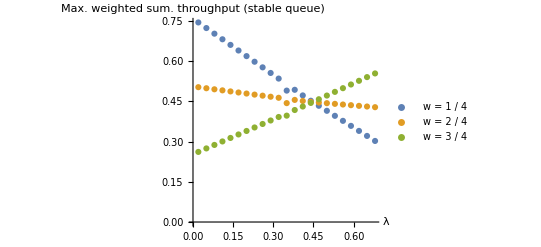

```mathematica
maxWeightedSum24=Table[ {N[lambda/100], T[lambda/100, 2/4][[1]] },{lambda, 2,68,3}]

maxWeightedSum34=Table[ {N[lambda/100], T[lambda/100, 3/4][[1]] },{lambda, 2,68,3}]
maxPlot = ListPlot[ {maxWeightedSum14, maxWeightedSum24, maxWeightedSum34}, AxesLabel->{ Style["λ", Italic,14], Style["Max. weighted sum. throughput (stable queue)", Italic, 12]}, AxesStyle->Thick,PlotLegends->{"w = 1 / 4","w = 2 / 4","w = 3 / 4"}]
```

```mathematica
maxWeightedSum34
```

```mathematica
Export2PDF[PlotName_]:=Module[{A=600},Export[SystemDialogInput["FileSave",StringJoin[{ToString[FileName],".eps"}]],PlotName,"AllowRasterization"->True,ImageSize->Full  ,ImageResolution->500]]
```

```mathematica
Export2PDF[maxPlot]
```

/Users/yannis/Desktop/My papers/Multiple Caching Helper/Figures/maxWeightedSumThroughput.eps

### Maximum Weighted Sum Throughputs Case w = 1/4:

```mathematica
w1= 1/4;
results1 = Table[ T[lambda/100,w1], {lambda,1, 68}];
results14=Table[  
{N[ lambda/100 ,2 ], 
N[ results1[[lambda]][[1]],3],
SetPrecision[ results1[[lambda]][[2]][[1]], 2],
SetPrecision[ results1[[lambda]][[2]][[2]], 2], 
SetPrecision[ results1[[lambda]][[2]][[3]] ,2 ]
 },{lambda, 1,68}]
```

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {39/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {2/5-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

NMaximize::incst: NMaximize was unable to generate any initial points satisfying the inequality constraints {41/100-0.350245 qs-0.0754212 qd qs≤0}. The initial region specified may not contain any feasible points. Changing the initial region or specifying explicit initial points may provide a better solution.

General::stop: Further output of NMaximize::incst will be suppressed during this calculation.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {43/100-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {11/25-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

NMaximize::nosat: Obtained solution does not satisfy the following constraints within Tolerance -> 0.001: {9/20-(0.11+0.244889 (1-0.176 qd)+0.12 qd) qs≤0}.

General::stop: Further output of NMaximize::nosat will be suppressed during this calculation.

{{0.01,0.751227,qs→1.,qd→1.,qc→0},{0.02,0.744249,qs→1.,qd→1.,qc→0},{0.03,0.737271,qs→1.,qd→1.,qc→0},{0.04,0.730293,qs→1.,qd→1.,qc→0},{0.05,0.723315,qs→1.,qd→1.,qc→0},{0.06,0.716337,qs→1.,qd→1.,qc→-1.9×10^-28},{0.07,0.709359,qs→1.,qd→1.,qc→0},{0.08,0.702381,qs→1.,qd→1.,qc→0},{0.09,0.695402,qs→1.,qd→1.,qc→0},{0.1,0.688424,qs→1.,qd→1.,qc→-3.8×10^-26},{0.11,0.681446,qs→1.,qd→1.,qc→0},{0.12,0.674468,qs→1.,qd→1.,qc→-8.7×10^-28},{0.13,0.66749,qs→1.,qd→1.,qc→0},{0.14,0.660512,qs→1.,qd→1.,qc→0},{0.15,0.653534,qs→1.,qd→1.,qc→0},{0.16,0.646556,qs→1.,qd→1.,qc→0},{0.17,0.639578,qs→1.,qd→1.,qc→-4.6×10^-22},{0.18,0.632599,qs→1.,qd→1.,qc→0},{0.19,0.625621,qs→1.,qd→1.,qc→0},{0.2,0.618643,qs→1.,qd→1.,qc→-6.1×10^-17},{0.21,0.611665,qs→1.,qd→1.,qc→0},{0.22,0.604687,qs→1.,qd→1.,qc→-3.7×10^-16},{0.23,0.597709,qs→1.,qd→1.,qc→-4.9×10^-18},{0.24,0.590731,qs→1.,qd→1.,qc→0},{0.25,0.583753,qs→1.,qd→1.,qc→0},{0.26,0.576775,qs→1.,qd→1.,qc→0},{0.27,0.569797,qs→1.,qd→1.,qc→0},{0.28,0.562818,qs→1.,qd→1.,qc→0},{0.29,0.55584,qs→1.,qd→1.,qc→-6.2×10^-19},{0.3,0.548862,qs→1.,qd→1.,qc→-4.9×10^-18},{0.31,0.541884,qs→1.,qd→1.,qc→0},{0.32,0.534906,qs→1.,qd→1.,qc→0},{0.33,0.527928,qs→1.,qd→1.,qc→-2.7×10^-27},{0.34,0.52095,qs→1.,qd→1.,qc→0},{0.35,0.490045,qs→1.,qd→0,qc→0},{0.36,0.48634,qs→1.,qd→0.13,qc→1.},{0.37,0.500016,qs→1.,qd→1.,qc→2.7×10^-9},{0.38,0.493037,qs→1.,qd→1.,qc→9.1×10^-6},{0.39,0.486059,qs→1.,qd→1.,qc→0},{0.4,0.479081,qs→1.,qd→1.,qc→0},{0.41,0.472103,qs→1.,qd→1.,qc→0},{0.42,0.465125,qs→1.,qd→1.,qc→0},{0.43,0.458464,qs→1.,qd→1.,qc→1.},{0.44,0.452217,qs→1.,qd→1.,qc→1.},{0.45,0.445971,qs→1.,qd→1.,qc→1.},{0.46,0.439724,qs→1.,qd→1.,qc→1.},{0.47,0.433478,qs→1.,qd→1.,qc→1.},{0.48,0.427231,qs→1.,qd→1.,qc→1.},{0.49,0.420985,qs→1.,qd→1.,qc→1.},{0.5,0.414738,qs→1.,qd→1.,qc→1.},{0.51,0.408492,qs→1.,qd→1.,qc→1.},{0.52,0.402245,qs→1.,qd→1.,qc→1.},{0.53,0.395999,qs→1.,qd→1.,qc→1.},{0.54,0.389752,qs→1.,qd→1.,qc→1.},{0.55,0.383506,qs→1.,qd→1.,qc→1.},{0.56,0.377259,qs→1.,qd→1.,qc→1.},{0.57,0.371013,qs→1.,qd→1.,qc→1.},{0.58,0.364766,qs→1.,qd→1.,qc→1.},{0.59,0.35852,qs→1.,qd→1.,qc→1.},{0.6,0.352273,qs→1.,qd→1.,qc→1.},{0.61,0.346027,qs→1.,qd→1.,qc→1.},{0.62,0.33978,qs→1.,qd→1.,qc→1.},{0.63,0.333534,qs→1.,qd→1.,qc→1.},{0.64,0.327287,qs→1.,qd→1.,qc→1.},{0.65,0.321041,qs→1.,qd→1.,qc→1.},{0.66,0.314794,qs→1.,qd→1.,qc→1.},{0.67,0.308548,qs→1.,qd→1.,qc→1.},{0.68,0.302301,qs→1.,qd→1.,qc→1.}}

```mathematica
TableForm[ results14, TableHeadings->{None,{"λ","max w(sum)"}} ]
```

λ | max w(sum) |  |  | 
0.01 | 0.751227 | qs→1. | qd→1. | qc→0
0.02 | 0.744249 | qs→1. | qd→1. | qc→0
0.03 | 0.737271 | qs→1. | qd→1. | qc→0
0.04 | 0.730293 | qs→1. | qd→1. | qc→0
0.05 | 0.723315 | qs→1. | qd→1. | qc→0
0.06 | 0.716337 | qs→1. | qd→1. | qc→-1.9×10^-28
0.07 | 0.709359 | qs→1. | qd→1. | qc→0
0.08 | 0.702381 | qs→1. | qd→1. | qc→0
0.09 | 0.695402 | qs→1. | qd→1. | qc→0
0.1 | 0.688424 | qs→1. | qd→1. | qc→-3.8×10^-26
0.11 | 0.681446 | qs→1. | qd→1. | qc→0
0.12 | 0.674468 | qs→1. | qd→1. | qc→-8.7×10^-28
0.13 | 0.66749 | qs→1. | qd→1. | qc→0
0.14 | 0.660512 | qs→1. | qd→1. | qc→0
0.15 | 0.653534 | qs→1. | qd→1. | qc→0
0.16 | 0.646556 | qs→1. | qd→1. | qc→0
0.17 | 0.639578 | qs→1. | qd→1. | qc→-4.6×10^-22
0.18 | 0.632599 | qs→1. | qd→1. | qc→0
0.19 | 0.625621 | qs→1. | qd→1. | qc→0
0.2 | 0.618643 | qs→1. | qd→1. | qc→-6.1×10^-17
0.21 | 0.611665 | qs→1. | qd→1. | qc→0
0.22 | 0.604687 | qs→1. | qd→1. | qc→-3.7×10^-16
0.23 | 0.597709 | qs→1. | qd→1. | qc→-4.9×10^-18
0.24 | 0.590731 | qs→1. | qd→1. | qc→0
0.25 | 0.583753 | qs→1. | qd→1. | qc→0
0.26 | 0.576775 | qs→1. | qd→1. | qc→0
0.27 | 0.569797 | qs→1. | qd→1. | qc→0
0.28 | 0.562818 | qs→1. | qd→1. | qc→0
0.29 | 0.55584 | qs→1. | qd→1. | qc→-6.2×10^-19
0.3 | 0.548862 | qs→1. | qd→1. | qc→-4.9×10^-18
0.31 | 0.541884 | qs→1. | qd→1. | qc→0
0.32 | 0.534906 | qs→1. | qd→1. | qc→0
0.33 | 0.527928 | qs→1. | qd→1. | qc→-2.7×10^-27
0.34 | 0.52095 | qs→1. | qd→1. | qc→0
0.35 | 0.490045 | qs→1. | qd→0 | qc→0
0.36 | 0.48634 | qs→1. | qd→0.13 | qc→1.
0.37 | 0.500016 | qs→1. | qd→1. | qc→2.7×10^-9
0.38 | 0.493037 | qs→1. | qd→1. | qc→9.1×10^-6
0.39 | 0.486059 | qs→1. | qd→1. | qc→0
0.4 | 0.479081 | qs→1. | qd→1. | qc→0
0.41 | 0.472103 | qs→1. | qd→1. | qc→0
0.42 | 0.465125 | qs→1. | qd→1. | qc→0
0.43 | 0.458464 | qs→1. | qd→1. | qc→1.
0.44 | 0.452217 | qs→1. | qd→1. | qc→1.
0.45 | 0.445971 | qs→1. | qd→1. | qc→1.
0.46 | 0.439724 | qs→1. | qd→1. | qc→1.
0.47 | 0.433478 | qs→1. | qd→1. | qc→1.
0.48 | 0.427231 | qs→1. | qd→1. | qc→1.
0.49 | 0.420985 | qs→1. | qd→1. | qc→1.
0.5 | 0.414738 | qs→1. | qd→1. | qc→1.
0.51 | 0.408492 | qs→1. | qd→1. | qc→1.
0.52 | 0.402245 | qs→1. | qd→1. | qc→1.
0.53 | 0.395999 | qs→1. | qd→1. | qc→1.
0.54 | 0.389752 | qs→1. | qd→1. | qc→1.
0.55 | 0.383506 | qs→1. | qd→1. | qc→1.
0.56 | 0.377259 | qs→1. | qd→1. | qc→1.
0.57 | 0.371013 | qs→1. | qd→1. | qc→1.
0.58 | 0.364766 | qs→1. | qd→1. | qc→1.
0.59 | 0.35852 | qs→1. | qd→1. | qc→1.
0.6 | 0.352273 | qs→1. | qd→1. | qc→1.
0.61 | 0.346027 | qs→1. | qd→1. | qc→1.
0.62 | 0.33978 | qs→1. | qd→1. | qc→1.
0.63 | 0.333534 | qs→1. | qd→1. | qc→1.
0.64 | 0.327287 | qs→1. | qd→1. | qc→1.
0.65 | 0.321041 | qs→1. | qd→1. | qc→1.
0.66 | 0.314794 | qs→1. | qd→1. | qc→1.
0.67 | 0.308548 | qs→1. | qd→1. | qc→1.
0.68 | 0.302301 | qs→1. | qd→1. | qc→1.

Case w = 2 / 4

```mathematica
w2 = 2/4;
results2 = Table[ T[lambda/100,w2], {lambda,1, 68}];
results24=Table[  
{N[ lambda/100 ,2 ], 
N[ results2[[lambda]][[1]],3],
SetPrecision[ results2[[lambda]][[2]][[1]], 2],
SetPrecision[ results2[[lambda]][[2]][[2]], 2], 
SetPrecision[ results2[[lambda]][[2]][[3]] ,2 ]
 },{lambda, 1,68}];
```

```mathematica
TableForm[ results24, TableHeadings->{None,{"λ","max w(sum)"}} ]
```

λ | max w(sum) |  |  | 
0.01 | 0.504151 | qs→1. | qd→1. | qc→0
0.02 | 0.502833 | qs→1. | qd→1. | qc→0
0.03 | 0.501514 | qs→1. | qd→1. | qc→0
0.04 | 0.500195 | qs→1. | qd→1. | qc→0
0.05 | 0.498877 | qs→1. | qd→1. | qc→0
0.06 | 0.497558 | qs→1. | qd→1. | qc→-2.×10^-28
0.07 | 0.496239 | qs→1. | qd→1. | qc→0
0.08 | 0.49492 | qs→1. | qd→1. | qc→0
0.09 | 0.493602 | qs→1. | qd→1. | qc→0
0.1 | 0.492283 | qs→1. | qd→1. | qc→-3.9×10^-26
0.11 | 0.490964 | qs→1. | qd→1. | qc→0
0.12 | 0.489645 | qs→1. | qd→1. | qc→-8.8×10^-28
0.13 | 0.488327 | qs→1. | qd→1. | qc→0
0.14 | 0.487008 | qs→1. | qd→1. | qc→0
0.15 | 0.485689 | qs→1. | qd→1. | qc→0
0.16 | 0.48437 | qs→1. | qd→1. | qc→0
0.17 | 0.483052 | qs→1. | qd→1. | qc→-4.7×10^-22
0.18 | 0.481733 | qs→1. | qd→1. | qc→0
0.19 | 0.480414 | qs→1. | qd→1. | qc→0
0.2 | 0.479096 | qs→1. | qd→1. | qc→-6.2×10^-17
0.21 | 0.477777 | qs→1. | qd→1. | qc→-3.2×10^-20
0.22 | 0.476458 | qs→1. | qd→1. | qc→-3.7×10^-16
0.23 | 0.475139 | qs→1. | qd→1. | qc→-5.×10^-18
0.24 | 0.473821 | qs→1. | qd→1. | qc→0
0.25 | 0.472502 | qs→1. | qd→1. | qc→0
0.26 | 0.471183 | qs→1. | qd→1. | qc→0
0.27 | 0.469864 | qs→1. | qd→1. | qc→0
0.28 | 0.468546 | qs→1. | qd→1. | qc→0
0.29 | 0.467227 | qs→1. | qd→1. | qc→-6.9×10^-19
0.3 | 0.465908 | qs→1. | qd→1. | qc→0
0.31 | 0.464589 | qs→1. | qd→1. | qc→-9.9×10^-28
0.32 | 0.463271 | qs→1. | qd→1. | qc→-2.3×10^-24
0.33 | 0.461952 | qs→1. | qd→1. | qc→0
0.34 | 0.460633 | qs→1. | qd→1. | qc→0
0.35 | 0.443364 | qs→1. | qd→0 | qc→0
0.36 | 0.444227 | qs→1. | qd→0.13 | qc→1.
0.37 | 0.456677 | qs→1. | qd→1. | qc→1.5×10^-7
0.38 | 0.455358 | qs→1. | qd→1. | qc→0
0.39 | 0.45404 | qs→1. | qd→1. | qc→0
0.4 | 0.452721 | qs→1. | qd→1. | qc→0
0.41 | 0.451402 | qs→1. | qd→1. | qc→0
0.42 | 0.450083 | qs→1. | qd→1. | qc→0
0.43 | 0.448976 | qs→1. | qd→1. | qc→1.
0.44 | 0.448145 | qs→1. | qd→1. | qc→1.
0.45 | 0.447314 | qs→1. | qd→1. | qc→1.
0.46 | 0.446483 | qs→1. | qd→1. | qc→1.
0.47 | 0.445652 | qs→1. | qd→1. | qc→1.
0.48 | 0.444821 | qs→1. | qd→1. | qc→1.
0.49 | 0.44399 | qs→1. | qd→1. | qc→1.
0.5 | 0.443159 | qs→1. | qd→1. | qc→1.
0.51 | 0.442328 | qs→1. | qd→1. | qc→1.
0.52 | 0.441497 | qs→1. | qd→1. | qc→1.
0.53 | 0.440666 | qs→1. | qd→1. | qc→1.
0.54 | 0.439835 | qs→1. | qd→1. | qc→1.
0.55 | 0.439004 | qs→1. | qd→1. | qc→1.
0.56 | 0.438173 | qs→1. | qd→1. | qc→1.
0.57 | 0.437342 | qs→1. | qd→1. | qc→1.
0.58 | 0.436511 | qs→1. | qd→1. | qc→1.
0.59 | 0.43568 | qs→1. | qd→1. | qc→1.
0.6 | 0.434849 | qs→1. | qd→1. | qc→1.
0.61 | 0.434018 | qs→1. | qd→1. | qc→1.
0.62 | 0.433187 | qs→1. | qd→1. | qc→1.
0.63 | 0.432356 | qs→1. | qd→1. | qc→1.
0.64 | 0.431525 | qs→1. | qd→1. | qc→1.
0.65 | 0.430694 | qs→1. | qd→1. | qc→1.
0.66 | 0.429863 | qs→1. | qd→1. | qc→1.
0.67 | 0.429032 | qs→1. | qd→1. | qc→1.
0.68 | 0.428201 | qs→1. | qd→1. | qc→1.

```mathematica
Case w = 3 / 4;
```

Set::write: Tag Times in Case w is Protected.

```mathematica
w3 = 3/4
results3 = Table[ T[lambda/100,w3], {lambda,1, 68}];
results34=Table[  
{N[ lambda/100 ,2 ], 
N[ results3[[lambda]][[1]],3],
SetPrecision[ results3[[lambda]][[2]][[1]], 2],
SetPrecision[ results3[[lambda]][[2]][[2]], 2], 
SetPrecision[ results3[[lambda]][[2]][[3]],2 ]
 },{lambda, 1,68}];

TableForm[ results34, TableHeadings->{None,{"λ","max w(sum)"}} ]
```

3/4

λ | max w(sum) |  |  | 
0.01 | 0.257076 | qs→1. | qd→1. | qc→0
0.02 | 0.261416 | qs→1. | qd→1. | qc→0
0.03 | 0.265757 | qs→1. | qd→1. | qc→0
0.04 | 0.270098 | qs→1. | qd→1. | qc→0
0.05 | 0.274438 | qs→1. | qd→1. | qc→0
0.06 | 0.278779 | qs→1. | qd→1. | qc→-2.×10^-28
0.07 | 0.28312 | qs→1. | qd→1. | qc→0
0.08 | 0.28746 | qs→1. | qd→1. | qc→0
0.09 | 0.291801 | qs→1. | qd→1. | qc→0
0.1 | 0.296141 | qs→1. | qd→1. | qc→-3.9×10^-26
0.11 | 0.300482 | qs→1. | qd→1. | qc→0
0.12 | 0.304823 | qs→1. | qd→1. | qc→-9.×10^-28
0.13 | 0.309163 | qs→1. | qd→1. | qc→0
0.14 | 0.313504 | qs→1. | qd→1. | qc→0
0.15 | 0.317845 | qs→1. | qd→1. | qc→0
0.16 | 0.322185 | qs→1. | qd→1. | qc→0
0.17 | 0.326526 | qs→1. | qd→1. | qc→-4.7×10^-22
0.18 | 0.330866 | qs→1. | qd→1. | qc→0
0.19 | 0.335207 | qs→1. | qd→1. | qc→0
0.2 | 0.339548 | qs→1. | qd→1. | qc→0
0.21 | 0.343888 | qs→1. | qd→1. | qc→-3.3×10^-20
0.22 | 0.348229 | qs→1. | qd→1. | qc→-3.7×10^-16
0.23 | 0.35257 | qs→1. | qd→1. | qc→-5.×10^-18
0.24 | 0.35691 | qs→1. | qd→1. | qc→0
0.25 | 0.361251 | qs→1. | qd→1. | qc→0
0.26 | 0.365592 | qs→1. | qd→1. | qc→0
0.27 | 0.369932 | qs→1. | qd→1. | qc→0
0.28 | 0.374273 | qs→1. | qd→1. | qc→0
0.29 | 0.378613 | qs→1. | qd→1. | qc→-7.7×10^-19
0.3 | 0.382954 | qs→1. | qd→1. | qc→-5.×10^-18
0.31 | 0.387295 | qs→1. | qd→1. | qc→0
0.32 | 0.391635 | qs→1. | qd→1. | qc→-2.4×10^-24
0.33 | 0.395976 | qs→1. | qd→1. | qc→-2.8×10^-27
0.34 | 0.400317 | qs→1. | qd→1. | qc→0
0.35 | 0.396682 | qs→1. | qd→0 | qc→0
0.36 | 0.402113 | qs→1. | qd→0.13 | qc→1.
0.37 | 0.413339 | qs→1. | qd→1. | qc→1.6×10^-6
0.38 | 0.417679 | qs→1. | qd→1. | qc→-2.7×10^-25
0.39 | 0.42202 | qs→1. | qd→1. | qc→-4.2×10^-28
0.4 | 0.42636 | qs→1. | qd→1. | qc→0
0.41 | 0.430701 | qs→1. | qd→1. | qc→0
0.42 | 0.435042 | qs→1. | qd→1. | qc→-3.3×10^-29
0.43 | 0.439488 | qs→1. | qd→1. | qc→1.
0.44 | 0.444072 | qs→1. | qd→1. | qc→1.
0.45 | 0.448657 | qs→1. | qd→1. | qc→1.
0.46 | 0.453241 | qs→1. | qd→1. | qc→1.
0.47 | 0.457826 | qs→1. | qd→1. | qc→1.
0.48 | 0.46241 | qs→1. | qd→1. | qc→1.
0.49 | 0.466995 | qs→1. | qd→1. | qc→1.
0.5 | 0.471579 | qs→1. | qd→1. | qc→1.
0.51 | 0.476164 | qs→1. | qd→1. | qc→1.
0.52 | 0.480748 | qs→1. | qd→1. | qc→1.
0.53 | 0.485333 | qs→1. | qd→1. | qc→1.
0.54 | 0.489917 | qs→1. | qd→1. | qc→1.
0.55 | 0.494502 | qs→1. | qd→1. | qc→1.
0.56 | 0.499086 | qs→1. | qd→1. | qc→1.
0.57 | 0.503671 | qs→1. | qd→1. | qc→1.
0.58 | 0.508255 | qs→1. | qd→1. | qc→1.
0.59 | 0.51284 | qs→1. | qd→1. | qc→1.
0.6 | 0.517424 | qs→1. | qd→1. | qc→1.
0.61 | 0.522009 | qs→1. | qd→1. | qc→1.
0.62 | 0.526593 | qs→1. | qd→1. | qc→1.
0.63 | 0.531178 | qs→1. | qd→1. | qc→1.
0.64 | 0.535762 | qs→1. | qd→1. | qc→1.
0.65 | 0.540347 | qs→1. | qd→1. | qc→1.
0.66 | 0.544931 | qs→1. | qd→1. | qc→1.
0.67 | 0.549516 | qs→1. | qd→1. | qc→1.
0.68 | 0.5541 | qs→1. | qd→1. | qc→1.